```mathematica
(*Requires Mathematica 10.2 - Schrodinger 1-D solution using  NDEigensystem - http://mathematica.stackexchange.com/questions/3229
3/find-eigen-energies-of-time-independent-schr%C3%B6dinger-equation *)
```

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]},u[x],{x,-10,10},8,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.005}}}}];
{egnVal2,egnVec2}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x],DirichletCondition[u[x]==0,True]},u[x],{x,-10,10},8];
```

```mathematica
egnVal=Riffle[egnVal1,egnVal2]
```

{0.5,0.501189,1.5,1.50696,2.5,2.53003,3.5,3.53334,4.5,4.68703,5.5,5.53289,6.5,7.059,7.5,7.83234}

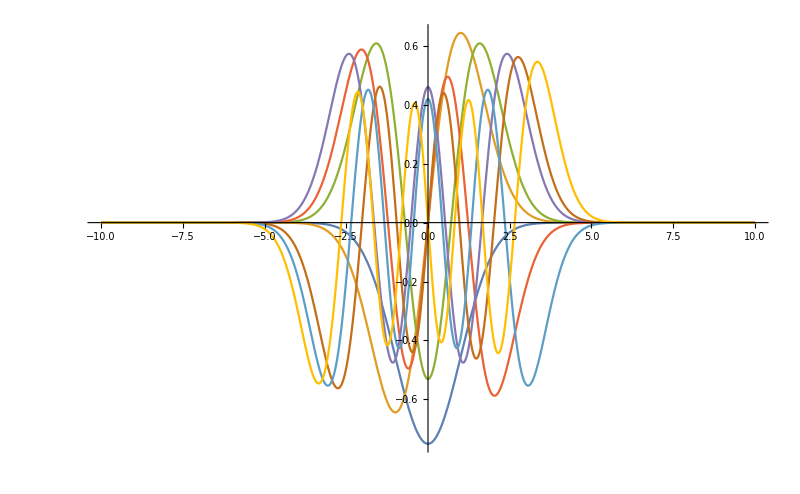

```mathematica
Plot[Evaluate@Table[egnVec1[[i]],{i,1,8}],{x,-10,10}, PlotRange->All,ImageSize->800]
```

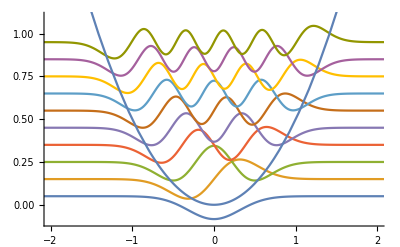

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5}

```mathematica
h=1/10;m=1;V[1,x_]:=1/2x^2;V[2,x_]:=1/2x^2+1/8x^4;V[3,x_]:=1/2x^2+1/8x^4+1/16x^6
ℒ={-h^2*(1/(2m))*u''[x]+V[1,x]*u[x],-h^2*(1/(2m))*u''[x]+V[2,x]*u[x],-h^2*(1/(2m))*u''[x]+V[3,x]*u[x]};
{vals,funs}=NDEigensystem[ℒ[[1]],u[x],{x,-10,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.005}}}}];
Show[Plot[Evaluate[h*funs+vals],{x,-3,3}],Plot[V[1,x],{x,-3,3}],PlotRange->{{-2,2},{-0.1,1.1}},AxesOrigin->{-3,0}]
vals*(h^-1)
```

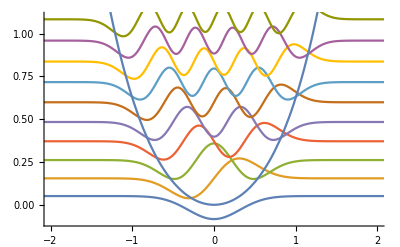

{0.509001,1.54405,2.6118,3.70971,4.83571,5.98805,7.16525,8.36603,9.58925,10.8339}

```mathematica
{vals,funs}=NDEigensystem[ℒ[[2]],u[x],{x,-10,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.005}}}}];
Show[Plot[Evaluate[h*funs+vals],{x,-3,3}],Plot[V[2,x],{x,-3,3}],PlotRange->{{-2,2},{-0.1,1.1}},AxesOrigin->{-3,0}]
vals*(h^-1)
```

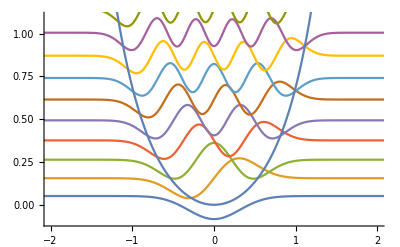

{0.510011,1.55065,2.63363,3.76053,4.93179,6.14718,7.40609,8.70769,10.051,11.4352}

Part::partd: Part specification ℒ⟦1⟧ is longer than depth of object.

ℒ⟦1⟧

```mathematica
{vals,funs}=NDEigensystem[ℒ[[3]],u[x],{x,-10,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.005}}}}];
Show[Plot[Evaluate[h*funs+vals],{x,-3,3}],Plot[V[3,x],{x,-3,3}],PlotRange->{{-2,2},{-0.1,1.1}},AxesOrigin->{-3,0}]
vals*(h^-1)
```